# Assignment 2

## 1.2.1

(1) Find, by hand,  three valid solutions to ((ⅆ^2 x)/(ⅆ t^2))^3=t x(t), x(0)=x'(0)=0. (Hint: Try solutions of the form a t^nfor some constants a and n.)

### Solution

Substitute x[t]=a t^n into the differential equation,

```mathematica
x[t_]=a*t^n
```

n
a t

```mathematica
x''[t]^3-t*x[t]
```

1 + n     3         3  3  -6 + 3 n
-(a t     ) + a  (-1 + n)  n  t

Indices of t are the same, which implies 1+n=-6+3n, which gives
n=7/2. Then solve for a:

```mathematica
Solve[(35/4)^3 a^3-a==0,a]
```

-8                   8
{{a -> 0}, {a -> -----------}, {a -> -----------}}
                 35 Sqrt[35]         35 Sqrt[35]

These are the three different possible solutions for the given initial conditions.

## 1.2.4

(4) A simple pendulum follows the differential equation θ''(t)=-g/lsin θ(t), where θ is the angle the pendulum makes with the vertical, g=9.8 m/s^2 is the acceleration of gravity, and l is the length of the pendulum. (See Fig. 1.8).

Fig. 1.8 Simple pendulum

Plot the direction field for this equation projected into the phase-space (θ,θ'), in the ranges -π < θ < π and -4 s^-1 < θ'  < 4 s^-1 , assuming a length l of 10 m.

(a) Discuss the qualitative features of the solutions. Do all phase-space trajectories circle the origin? If not, why not? What do these trajectories correspond to physically?

(b) Find the energy H for this motion in terms of θ and θ'. Plot several curves of constant H on top of your direction field, to verify that the field is tangent to them.

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
g=9.8; l=10;
```

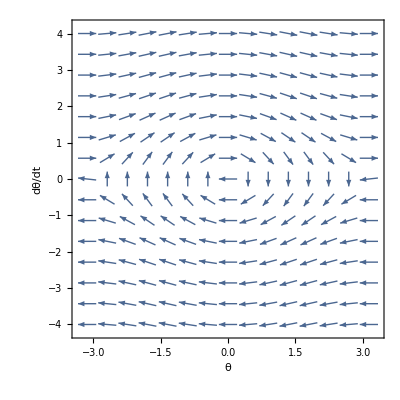

```mathematica
dfield = VectorPlot[{ω,-g/l Sin[θ]},{θ,-Pi,Pi},{ω,-4,4},Axes->True,AxesLabel->{"θ","dθ/dt"},VectorScale->{.04,.5,None}]
```

(a) Not all solutions circle the origin. Solutions that circle the origin correspond to oscillations of the pendulum back and forth; solutions that do not circle the origin correspond to full rotations of the pendulum.

(b) Energy H for the pendulum = kinetc + potential enegies. Kinetic energy = 1/2 m (ω l)^2, where ω = dθ/dt is the angular frequency. Potential energy is the energy of the mass in gravity,  m g z = m g l (1-cosθ). So H=1/2 m (ω l)^2+ m g l (1-cosθ).

```mathematica
H[θ_,ω_] = 1/2 m (ω l)^2 + m g l (1-Cos[θ]);
```

Take m=1; it's actual value is unimportant to the contour plots of H we are about to do:

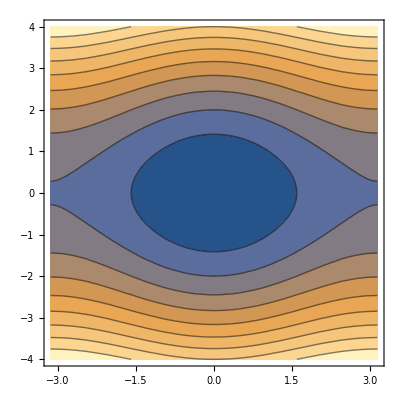

```mathematica
m=1;
ContourPlot[H[θ,ω],{θ,-Pi,Pi},{ω,-4,4}]
```

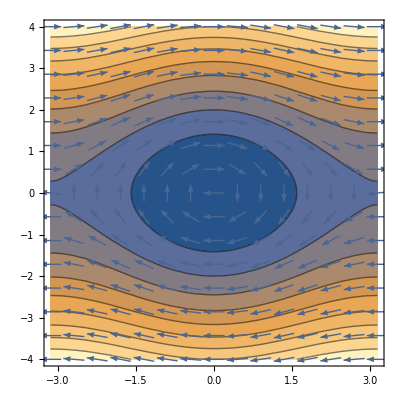

```mathematica
Show[%,dfield]
```

## 1.3.2

(2) A spaceship undergoing constant acceleration g=9.8 m/s^2 (as felt by the passengers) will follow Newton's second law, with the addition (by Einstein) that the apparent mass of the ship as seen by a stationary  observer will increase with velocity v(t) in proportion to the factor 1/√(1-v^2/c^2). This implies that the velocity satisfies the following first-order ODE:

ⅆ/ⅆt(v/(√(1-v^2/c^2)))=g.

(a)Find the general solution, using pencil and paper, for the position x(t) of the ship (where x(t) and v(t) are related in the usual way, by  v=ⅆ x/ⅆt).

(b) After 100 earth years of acceleration, starting from rest, how far has the ship gone in light-years (one light-year = 9.45 × 10^15m)?

(c) Thanks to relativistic time dilation, the amount of time τ  that has passed onboard the ship is considerably shorter than 100 years, and is given by the solution to the differential equation ⅆτ/ⅆt=√(1-(v(t))^2/c^2),τ(0)=0 . Solve this ODE, using DSolve and the solution for v(t) from part (b) above, to find the amount of time that has gone by for passengers on the ship. (Note: The nearest star is “only” about 4.3 light years from earth).  What was the average speed of the ship over the course of the trip, in units of c, as far as the passengers are concerned?

### Solution

```mathematica
Remove["Global`*"]
```

```mathematica
DSolve[{D[v[t]/Sqrt[1-(v[t]/c)^2],t]==g,v[0]==0},v[t],t]
```

{{v[t]→-(c g t)/(√(c^2+g^2 t^2))},{v[t]→(c g t)/(√(c^2+g^2 t^2))}}

```mathematica
Simplify[v[t]/.%[[2]],g>0&&c>0&&t>0]
```

(c g t)/(√(c^2+g^2 t^2))

```mathematica
v[t_] = %;
```

```mathematica
Clear[x]
```

```mathematica
DSolve[{x'[t]==v[t],x[0]==0},x[t],t]
```

{{x[t]→(-c √(c^2)+c √(c^2+g^2 t^2))/g}}

```mathematica
Simplify[x[t]/.%[[1]],c>0&&t>0&&g>0]
```

(c (-c+√(c^2+g^2 t^2)))/g

```mathematica
x[t_] = % + x0
```

(c (-c+√(c^2+g^2 t^2)))/g+x0

This is the solution for x(t) startying at x=x_0 and v=0. The solution after 100 years (earth time) is:

```mathematica
x[100 365 24 3600]-x0/.{  g->9.8 , c->3.*^8}
```

9.36941×10^17

```mathematica
%/(9.45*^15)
```

99.1472

The ship travels about 99 light years. The time passed on the ship is far less:

```mathematica
tau[t]/.DSolve[{tau'[t]==Sqrt[1-v[t]^2/c^2],tau[0]==0},tau[t],t][[1]]
```

(-√(c^2) Log[√(c^2) g]+√(c^2/(c^2+g^2 t^2)) √(c^2+g^2 t^2) Log[g^2 t+g √(c^2+g^2 t^2)])/g

```mathematica
τ[t_] = Simplify[%,c>0&&g>0&&t>0]
```

(c Log[(g t+√(c^2+g^2 t^2))/c])/g

```mathematica
τ[100  365 24 3600]/. { g->9.8 , c->3*^8}
```

1.63104×10^8

```mathematica
%/(365 24 3600)
```

5.172

For the passengers in the ship, it only takes 5.17 years to complete the trip . That's an average speed of 99/5.27 light years per year, or 19.1 c -- roughly 20 times the speed of light.

## 1.4.4

(4) Einstein's general theory of relativity generalizes Newton's theory of gravitation to encompass the situation where masses have large kinetic and/or potential energies (on the order of or larger than their rest masses). Even at low energies, the theory predicts a small correction to Newton's 1/r^2 force law:

f(r)=-G M(1/r^2+(3 L^2)/(c^2 r^4)),

where L is the specific angular momentum-- see Eq. (1.2.22). This force per unit mass replaces that which appears on the right-hand side of the orbit equation (1.3.5).

(a)Use NDSolve to determine the new orbit r(θ) predicted by this equation, and plot it for 0<θ < 4π, taking orbital parameters for the planet Mercury: r(0) =  46.00×10^6 km, (perihelion distance) r'(0)=0,  L = 2.713×10^15 m^2/s. The mass of the sun is 1.9891×10^30 kg.

(b) Show numerically  that the orbit no longer closes, and that each successive perihelion precesses by an amount Δθ . Find a numerical value for Δθ.   Be careful: the numerical integration must be performed very accurately! (The precession of Mercury's perihelion has been measured, and after successive refinements, removing extraneous effects, it was found to be in reasonable agreement with this result.)

### Solution

```mathematica
Clear["Global`*"]
```

```mathematica
L=2.713*10^15;M=1.9891*10^30;G=6.6726*10^-11;c=3*10^8;
```

let' s first do the problem at regular precision :

```mathematica
NDSolve[{(L/r[t]^2)D[L r'[t]/r[t]^2,t]-L^2/r[t]^3+G M(1/r[t]^2+3 L^2/(c^2 r[t]^4))==0,r[0]==46*10^9,r'[0]==0},r[t],{t,0,4 Pi}]
```

{{r[t]→InterpolatingFunction[{{0., 12.5664}}, <>][t]}}

```mathematica
r[t] /. %[[1]]
```

InterpolatingFunction[{{0., 12.5664}}, <>][t]

```mathematica
r[t_]=%;
```

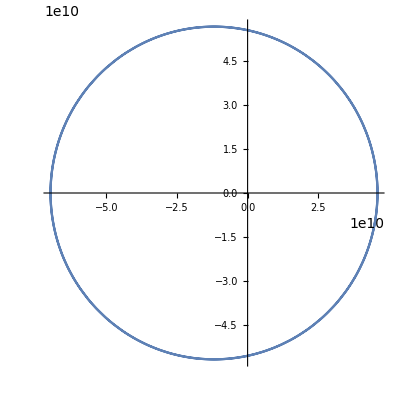

```mathematica
ParametricPlot[{r[t]Cos[t],r[t]Sin[t]},{t,0,4 Pi},AspectRatio->1]
```

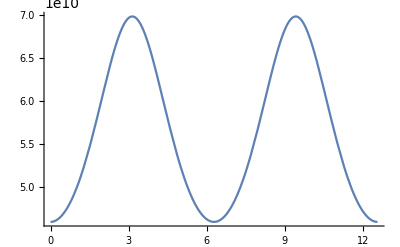

```mathematica
Plot[r[θ],{θ,0,4 Pi}]
```

Let' s look at the derivative of r near θ = 2 Pi :

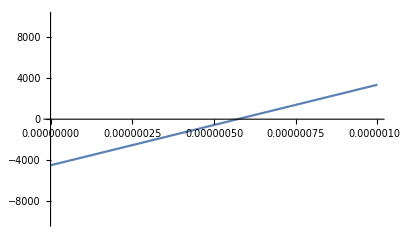

```mathematica
Plot[r'[t+2Pi],{t,-310^-6,10^-6},PlotRange->{-10^4,10^4}]
```

The first perihelion corresponds to θ = 0, the second one is where the crossing occurs above :

```mathematica
FindRoot[r'[t]==0,{t,2 Pi-2 10^-6}]
```

{t→6.28319}

and the perihelion appears to precess by :

```mathematica
(t/.%)-2 Pi
```

5.7227×10^-7

the observed value is 4.99*10^-7, which isn' t bad but lets see what happens with more accuracy. We need to increase the precision.

```mathematica
Clear[r]
```

```mathematica
NDSolve[{(L/r[t]^2)D[L r'[t]/r[t]^2,t]-L^2/r[t]^3+G M(1/r[t]^2+3 L^2/(c^2 r[t]^4))==0,r[0]==46*10^9,r'[0]==0},r[t],{t,0,4 Pi},AccuracyGoal->13,PrecisionGoal->13,MaxSteps->5000]
```

{{r[t]→InterpolatingFunction[{{0., 12.5664}}, <>][t]}}

```mathematica
r[t] /. %[[1]]
```

InterpolatingFunction[{{0., 12.5664}}, <>][t]

```mathematica
r[t_]=%;
```

```mathematica
FindRoot[r'[t]==0,{t,2 Pi},AccuracyGoal->11]
```

{t→6.28319}

and the perihelion appears to precess  in each orbit by :

```mathematica
(t/.%)-2 Pi
```

5.01259×10^-7

This is  closer to the observed value. Moral : if you need an accurate result, make sure you are integrating the equations accurately.

## 1.4.10(iii)

(10) Use Euler's method to

(a) solve the following ODEs with initial conditions over the given range of time, and for the given step size. Then,

(b) plot the solution;

(c) solve the ODE analytically, and plot the error in x(t);

(d) using the results of (c) predict how small a step size is necessary for the error to be smaller than 10^-4 over the course of the run.

(iii)	x'''+2 x''+x'+2x=cos t  x(0)=x'(0)=x''(0)=0, 0<t<20, Δt=0.02.

### Solution

#### (a,b)

We will use Eulers method for coupled first order ODES. This requires writing (iii) as 3 first order ODES, to whit:
x'=v,v'=a,a'=cos t - 2x - v - 2 a.  So our vector variable is z={x,v,a} and our vector force function is

```mathematica
Clear["Global`*"]
```

```mathematica
F[z_,t_] := {v,a,Cos[t]-2 x - v - 2 a}/.{x->z[[1]],v->z[[2]],a->z[[3]]}
```

Now apply Eulers method for the given step size:

```mathematica
Δt = 0.02;
```

```mathematica
t[n_] = n Δt;
```

```mathematica
Z[n_] :=Z[n]= Z[n-1] + Δt F[Z[n-1],t[n-1]]
```

```mathematica
Z[0] = {0,0,0};
```

To get to t=20, we need this many steps:

```mathematica
M = Floor[20/Δt]
```

1000

```mathematica
sol1 = Table[{t[n],Z[n][[1]]},{n,0,M}];
```

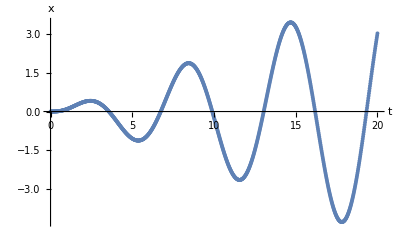

```mathematica
nsol1=ListPlot[sol1,AxesLabel->{"t","x"}]
```

#### (c,d)

```mathematica
DSolve[{x'''[t] + 2 x''[t] + x'[t] + 2x[t] == Cos[t],x[0]==x'[0]==x''[0]==0},x[t],t]
```

{{x[t]→1/100 ⅇ^(-2 t) (-8-12 ⅇ^(2 t) Cos[t]-10 ⅇ^(2 t) t Cos[t]+20 ⅇ^(2 t) Cos[t]^3-6 ⅇ^(2 t) Sin[t]+20 ⅇ^(2 t) t Sin[t]+10 ⅇ^(2 t) Cos[t]^2 Sin[t]-5 ⅇ^(2 t) Cos[t] Sin[2 t]+10 ⅇ^(2 t) Sin[t] Sin[2 t])}}

```mathematica
xs[t_] = x[t]/.%[[1]];
```

Interpolation of the previous numerical solution, for comparison

```mathematica
interp1 = Interpolation[sol1]
```

InterpolatingFunction[{{0., 20.}}, <>]

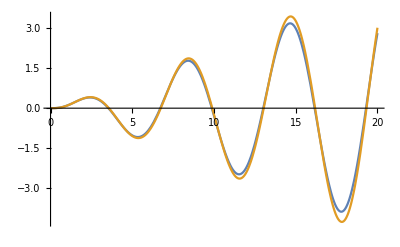

```mathematica
Plot[{xs[t],interp1[t]},{t,0,20}]
```

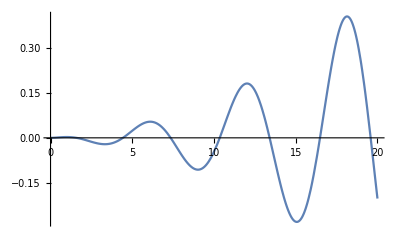

```mathematica
Plot[xs[t]-interp1[t],{t,0,20}]
```

Error grows to about 0.4! So to get down to 10^-4 with this method which is of order Δt, we require a reduction of Δt by a factor of 10^-4/.4

```mathematica
10^-4/.4
```

0.00025

Oy.

```mathematica
Δt = Δt*%
```

5.×10^-6

Yow. This is going to take a lot of steps!

```mathematica
M = Floor[20/%]
```

3999999

TO check, lets not run it this long. Lets run for 20 times less time. The error should be 20 times less than 10^-4 , since it appears to grow linearly with time.

```mathematica
Clear[Z]
```

```mathematica
t[n_] = n Δt;
```

```mathematica
Z[n_] :=Z[n]= Z[n-1] + Δt F[Z[n-1],t[n-1]]
```

```mathematica
Z[0] = {0,0,0};
```

```mathematica
sol2 = Table[{t[n],Z[n][[1]]},{n,0,M/20}];
```

```mathematica
interp2 = Interpolation[sol2]
```

InterpolatingFunction[{{0., 0.999995}}, <>]

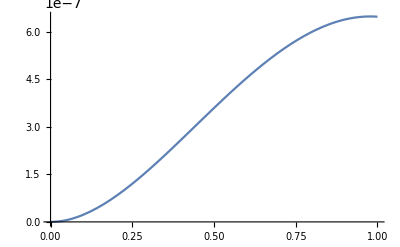

```mathematica
Plot[xs[t]-interp2[t],{t,0,.9999}]
```

error is around 7*10^-7 . about 10 times less than expected.

## 1.4.14(b)

(14) Modify our second-order predictor-corrector algorithm so that it can handle differential equations of order higher than one, or systems of coupled equations. Use the modified method to repeat

(b) Exercise (10)(iii),

### Solution

write 3rd order ODE as 3 coupled first order ODEs, just as in Euler’s method solution
ⅆx/ⅆt = v, ⅆv/ⅆt = a, ⅆa/ⅆt = -2a-v-2x+cos t. Therefore, ⅆz/ⅆt = f where
z=(x,v,a), f(t,z)=(v,a,-2a-v-2x+cos t).

```mathematica
f[t_,z_] := {v,a,-2a-v-2x+Cos[t]}/.{x->z[[1]],v->z[[2]],a->z[[3]]}
```

```mathematica
PCsol[z0_,time_,dt_]:=Module[{z,z1,f0},
t[n_]=n dt;
z[0]=z0;
f0:=f[t[n-1],z[n-1]];
z1:=z[n-1]+dt f0;
z[n_]:=z[n]=z[n-1]+dt (f0+f[t[n],z1])/2;
sol=Table[{t[n],z[n][[1]]},{n,0,time/dt}];
xPC=Interpolation[sol]]
```

```mathematica
PCsol[{0,0,0},20,.02]
```

InterpolatingFunction[{{0., 20.}}, <>]

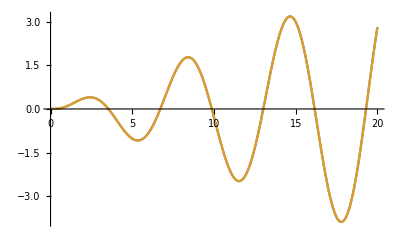

```mathematica
Plot[{xPC[t],xs[t]},{t,0,20}]
```

Much smaller error than in Euler’s method; maximum error is about 0.003:

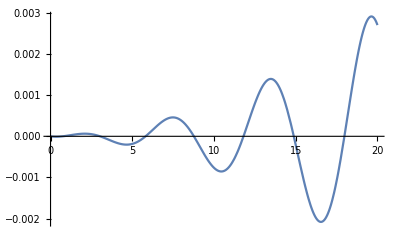

```mathematica
Plot[{xPC[t]-xs[t]},{t,0,20}]
```

To make the error as small as 10^-4, reduce Δt by factor

```mathematica
(10^-4/.003)//Sqrt
```

0.182574

(error scales as Δt^2)

```mathematica
PCsol[{0,0,0},20,.02 %]
```

InterpolatingFunction[{{0., 19.9992}}, <>]

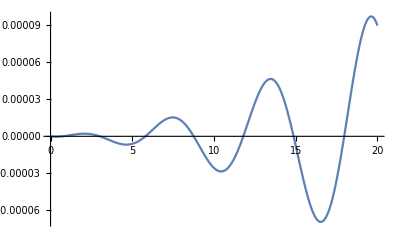

```mathematica
Plot[{xPC[t]-xs[t]},{t,0,20}]
```

Now error is less than 10^-4